# Statistische Analyse - Wunschgeschwindigkeit von Passanten

## Untersuchung auf Normalverteilung

### Extrahieren der Werte

```mathematica
holedate = SemanticImport["D:\\Dokumente\\Studium\\Master_Informatik\\Semester1\\ModellbildungSimulation\\hm-modellbildung\\angabe1\\data\\geschwindigkeiten.csv"]
```

Dataset[<>]

```mathematica
zeitenInEbene=holedata[Select[#"Ebene"=="x"&],"Zeit in sec"]
```

Dataset[<>]

```mathematica
zeitenTreppeRauf = holedata[Select[#"Treppe"=="auf"&],"Zeit in sec"]
```

Dataset[<>]

```mathematica
zeitenTreppeRunter = holedata[Select[#"Treppe"=="ab"&],"Zeit in sec"]
```

Dataset[<>]

### Erstellen der Histogramme

```mathematica
Manipulate[Histogram[zeitenInEbene,x],{x,1,20,1}]
```

```mathematica
Manipulate[Histogram[zeitenTreppeRauf,x],{x,1,20,1}]
```

```mathematica
Manipulate[Histogram[zeitenTreppeRunter,x],{x,1,20,1}]
```

### Überprüfung auf Normalverteilung

```mathematica
DistTestEbene=DistributionFitTest[Array[zeitenInEbene,39],Automatic,"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
DistTestTreppeAuf=DistributionFitTest[Array[zeitenTreppeRauf,39],Automatic,"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
DistTestTreppeAb=DistributionFitTest[Array[zeitenTreppeRunter,39],Automatic,"HypothesisTestData"]
```

HypothesisTestData[…]

Gesamte Test :

```mathematica
DistTestEbene["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 0.883263 | 0.0227031
Baringhaus-Henze | 0.583627 | 0.0684827
Cramér-von Mises | 0.102838 | 0.10178
Jarque-Bera ALM | 8.64552 | 0.04248
Mardia Combined | 8.64552 | 0.04248
Mardia Kurtosis | 1.12993 | 0.258506
Mardia Skewness | 5.23789 | 0.0221
Pearson χ^2 | 19.3846 | 0.00356106
Shapiro-Wilk | 0.916813 | 0.00694183

```mathematica
DistTestTreppeAuf["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 5.92884 | 1.33954×10^-7
Baringhaus-Henze | 6.49038 | 7.00629×10^-7
Cramér-von Mises | 1.03919 | 0.
Jarque-Bera ALM | 158.733 | 0.
Mardia Combined | 158.733 | 0.
Mardia Kurtosis | 8.18347 | 2.75779×10^-16
Mardia Skewness | 48.4211 | 3.43848×10^-12
Pearson χ^2 | 44.7692 | 5.20127×10^-8
Shapiro-Wilk | 0.577669 | 2.12556×10^-9

```mathematica
DistTestTreppeAb["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 3.81296 | 6.41017×10^-7
Baringhaus-Henze | 3.90038 | 0.0000190082
Cramér-von Mises | 0.654181 | 0.
Jarque-Bera ALM | 89.4773 | 0.000197035
Mardia Combined | 89.4773 | 0.000197035
Mardia Kurtosis | 5.96369 | 2.46609×10^-9
Mardia Skewness | 29.3662 | 5.9913×10^-8
Pearson χ^2 | 37.3846 | 1.48155×10^-6
Shapiro-Wilk | 0.717432 | 2.45626×10^-7

Fazit: Zeiten in der Ebene sind normalverteilt, Zeiten für Treppe rauf und runter hingegen nicht!

### Erstellung der Quantile

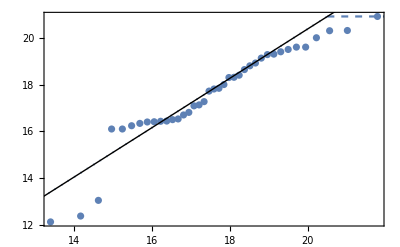

```mathematica
QuantilePlot[zeitenInEbene]
```

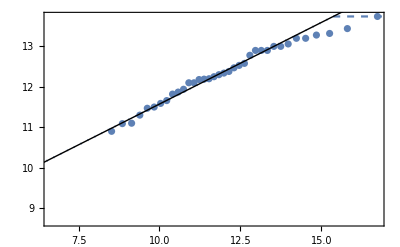

```mathematica
QuantilePlot[zeitenTreppeRauf]
```

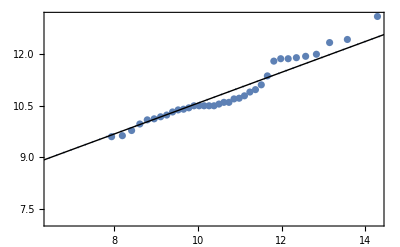

```mathematica
QuantilePlot[zeitenTreppeRunter]
```